## Load electricity price by state

Build the electricity price by state in time database.
Data from: https://www.eia.gov/electricity/monthly/epm_table_grapher.php?t=epmt_5_06_a

I will use a substitution rule to parse the state names in the database.

```mathematica
stateEntitiesRule = {"New England"->None,"Connecticut"->Entity["AdministrativeDivision",{"Connecticut","UnitedStates"}],"Maine"->Entity["AdministrativeDivision",{"Maine","UnitedStates"}],"Massachusetts"->Entity["AdministrativeDivision",{"Massachusetts","UnitedStates"}],"New Hampshire"->Entity["AdministrativeDivision",{"NewHampshire","UnitedStates"}],"Rhode Island"->Entity["AdministrativeDivision",{"RhodeIsland","UnitedStates"}],"Vermont"->Entity["AdministrativeDivision",{"Vermont","UnitedStates"}],"Middle Atlantic"->None,"New Jersey"->Entity["AdministrativeDivision",{"NewJersey","UnitedStates"}],"New York"->Entity["AdministrativeDivision",{"NewYork","UnitedStates"}],"Pennsylvania"->Entity["AdministrativeDivision",{"Pennsylvania","UnitedStates"}],"East North Central"->None,"Illinois"->Entity["AdministrativeDivision",{"Illinois","UnitedStates"}],"Indiana"->Entity["AdministrativeDivision",{"Indiana","UnitedStates"}],"Michigan"->Entity["AdministrativeDivision",{"Michigan","UnitedStates"}],"Ohio"->Entity["AdministrativeDivision",{"Ohio","UnitedStates"}],"Wisconsin"->Entity["AdministrativeDivision",{"Wisconsin","UnitedStates"}],"West North Central"->None,"Iowa"->Entity["AdministrativeDivision",{"Iowa","UnitedStates"}],"Kansas"->Entity["AdministrativeDivision",{"Kansas","UnitedStates"}],"Minnesota"->Entity["AdministrativeDivision",{"Minnesota","UnitedStates"}],"Missouri"->Entity["AdministrativeDivision",{"Missouri","UnitedStates"}],"Nebraska"->Entity["AdministrativeDivision",{"Nebraska","UnitedStates"}],"North Dakota"->Entity["AdministrativeDivision",{"NorthDakota","UnitedStates"}],"South Dakota"->Entity["AdministrativeDivision",{"SouthDakota","UnitedStates"}],"South Atlantic"->None,"Delaware"->Entity["AdministrativeDivision",{"Delaware","UnitedStates"}],"District of Columbia"->Entity["AdministrativeDivision",{"DistrictOfColumbia","UnitedStates"}],"Florida"->Entity["AdministrativeDivision",{"Florida","UnitedStates"}],"Georgia"->Entity["AdministrativeDivision",{"Georgia","UnitedStates"}],"Maryland"->Entity["AdministrativeDivision",{"Maryland","UnitedStates"}],"North Carolina"->Entity["AdministrativeDivision",{"NorthCarolina","UnitedStates"}],"South Carolina"->Entity["AdministrativeDivision",{"SouthCarolina","UnitedStates"}],"Virginia"->Entity["AdministrativeDivision",{"Virginia","UnitedStates"}],"West Virginia"->Entity["AdministrativeDivision",{"WestVirginia","UnitedStates"}],"East South Central"->None,"Alabama"->Entity["AdministrativeDivision",{"Alabama","UnitedStates"}],"Kentucky"->Entity["AdministrativeDivision",{"Kentucky","UnitedStates"}],"Mississippi"->Entity["AdministrativeDivision",{"Mississippi","UnitedStates"}],"Tennessee"->Entity["AdministrativeDivision",{"Tennessee","UnitedStates"}],"West South Central"->None,"Arkansas"->Entity["AdministrativeDivision",{"Arkansas","UnitedStates"}],"Louisiana"->Entity["AdministrativeDivision",{"Louisiana","UnitedStates"}],"Oklahoma"->Entity["AdministrativeDivision",{"Oklahoma","UnitedStates"}],"Texas"->Entity["AdministrativeDivision",{"Texas","UnitedStates"}],"Mountain"->None,"Arizona"->Entity["AdministrativeDivision",{"Arizona","UnitedStates"}],"Colorado"->Entity["AdministrativeDivision",{"Colorado","UnitedStates"}],"Idaho"->Entity["AdministrativeDivision",{"Idaho","UnitedStates"}],"Montana"->Entity["AdministrativeDivision",{"Montana","UnitedStates"}],"Nevada"->Entity["AdministrativeDivision",{"Nevada","UnitedStates"}],"New Mexico"->Entity["AdministrativeDivision",{"NewMexico","UnitedStates"}],"Utah"->Entity["AdministrativeDivision",{"Utah","UnitedStates"}],"Wyoming"->Entity["AdministrativeDivision",{"Wyoming","UnitedStates"}],"Pacific Contiguous"->None,"California"->Entity["AdministrativeDivision",{"California","UnitedStates"}],"Oregon"->Entity["AdministrativeDivision",{"Oregon","UnitedStates"}],"Washington"->Entity["AdministrativeDivision",{"Washington","UnitedStates"}],"Pacific Noncontiguous"->None,"Alaska"->Entity["AdministrativeDivision",{"Alaska","UnitedStates"}],"Hawaii"->Entity["AdministrativeDivision",{"Hawaii","UnitedStates"}],"U.S. Total"->None};
```

The database is separated into residential, commercial and industrial prices. The database is organized as it follows: Every directory correspond to the month when the survey was made, and the file Table_5_06_A contains electricity prices by state on a given month. There are 3 columns that correspond to residential, commercial and industrial prices.

I will focus on industrial prices since they are the least regulated. In this database prices come as Cents per Kilowatt/hour.

```mathematica
residential = 2;
commercial = 4;
industrial = 6;
directories = Select[FileNames["*",NotebookDirectory[]<>"ElectricityPrices"],FileType[#]==Directory&];

electricityPricesByDate = Table[
data = First[Import[d<>"/Table_5_06_A.xlsx"]];
date = DateObject[data[[4,2]]];
statesAndPrices = Take[data,{5,-3}];
entityStates = statesAndPrices[[All,1]] /. stateEntitiesRule;
statePrices =  DeleteCases[Transpose[{entityStates,statesAndPrices[[All,industrial]]}],{None,_}|{__String}];
{date,statePrices}

,{d,directories}
];
electricityPricesByDate = SortBy[electricityPricesByDate,First];
```

Visualization of electricity prices by date

```mathematica
Manipulate[
GeoRegionValuePlot[electricityPricesByDate[[i,2]],PlotLabel->DateString[electricityPricesByDate[[i,1]]],ImageSize->500,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Log[#/15+1]]&)],
{i,1,Length[electricityPricesByDate],1},
SaveDefinitions->True
]
```

Since the format of the database make it difficult to work with time series I will rearrange it.

```mathematica
states = electricityPricesByDate[[1,2,All,1]];
electricityPricesByState = Table[{
First[electricityPricesByDate[[All,2,i,1]]],Transpose[{electricityPricesByDate[[All,1]],electricityPricesByDate[[All,2,i]][[All,2]]}]},{i,1,Length[states]}
];

electricityPricesByState = DeleteCases[electricityPricesByState,{Entity["AdministrativeDivision",{"Alaska","UnitedStates"}],_}|{Entity["AdministrativeDivision",{"DistrictOfColumbia","UnitedStates"}],_}|{Entity["AdministrativeDivision",{"Hawaii","UnitedStates"}],_}];

electricityPricesByState = SortBy[electricityPricesByState,First];
```

With this I can plot the time series of every state

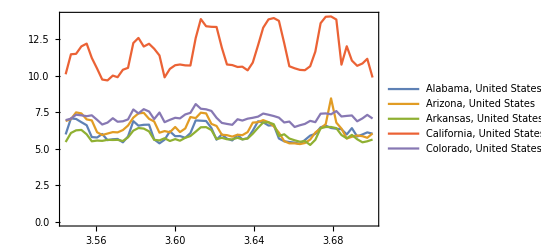
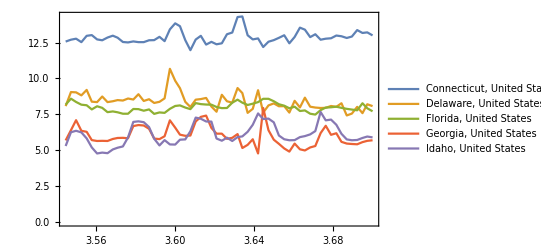
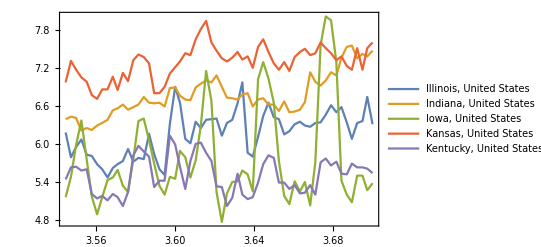
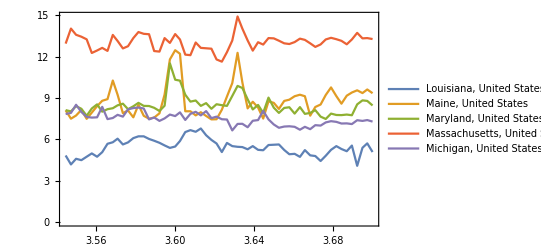
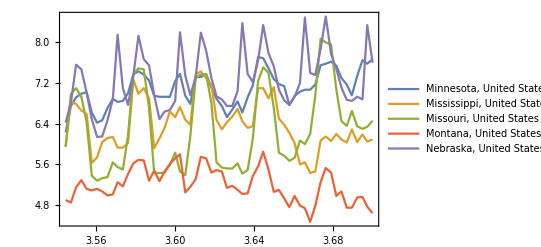
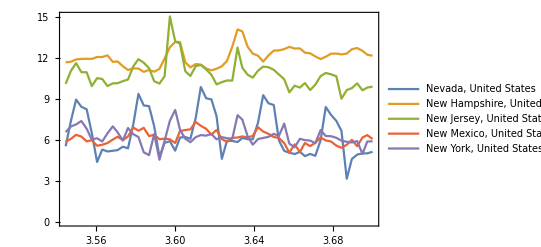
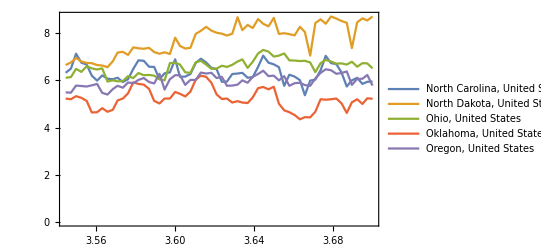
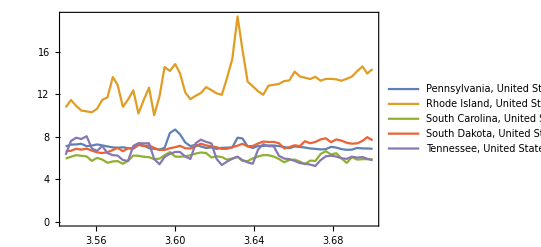
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
plots = Map[DateListPlot[#[[All,2]],PlotLegends->#[[All,1]]]&,Partition[electricityPricesByState,5]];
Grid[Partition[plots,UpTo[3]],Frame->All]
```

How are the prices on each state correlated?

From the time series it can be seen that some states have highly correlated prices. In order to identify the characteristics they share I plot the correlation matrix.

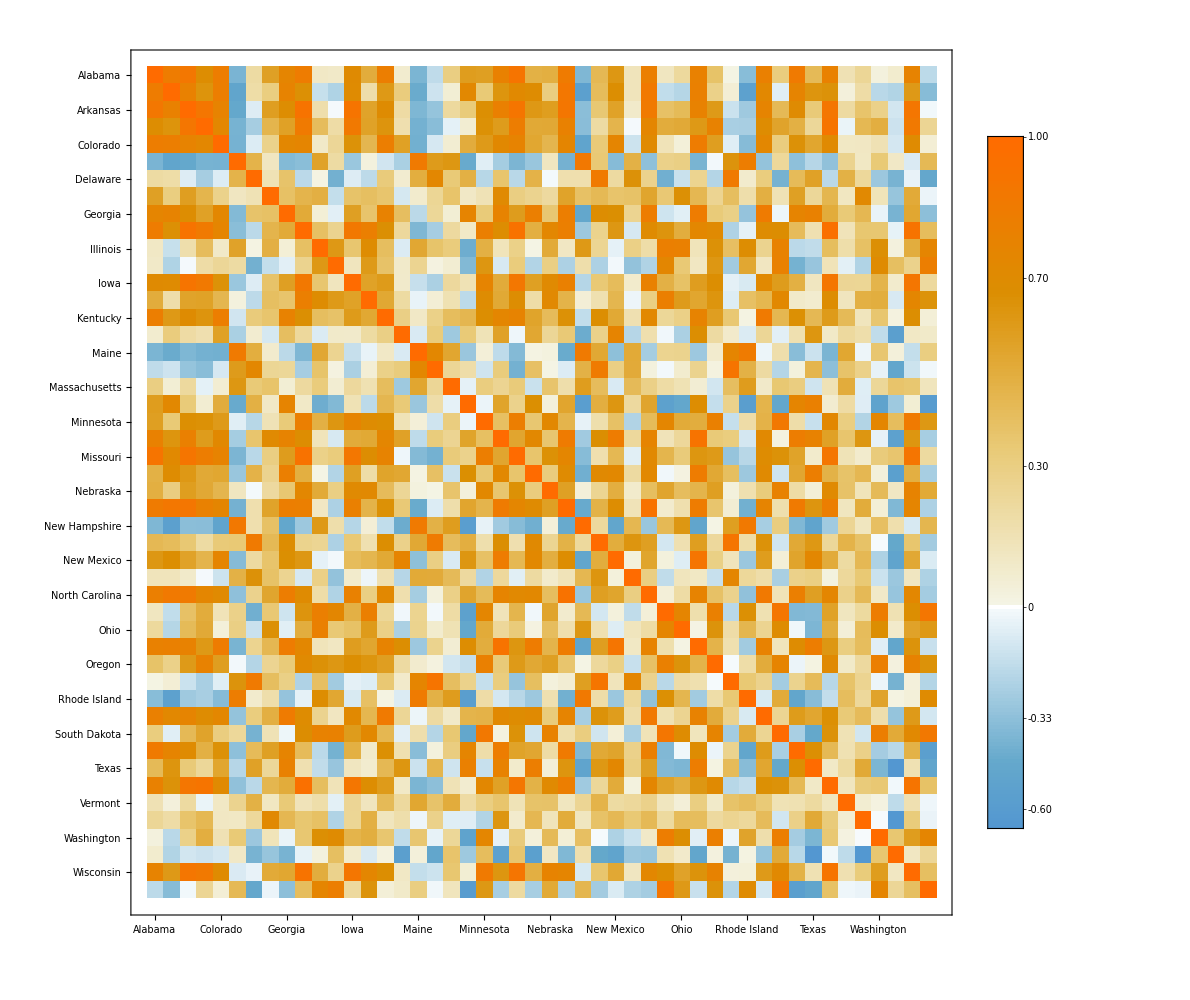

```mathematica
states = electricityPricesByState[[All,1]];
stateNames = Map[StringDelete[EntityValue[#,"Name"],", United States"]&,states];
prices = electricityPricesByState[[All,2,All,2]];
corrMatrix = Correlation[Transpose[prices]];

horizontalTicks = Transpose[{Range[Length[stateNames]],stateNames}];
verticalTicks = Transpose[{Range[Length[stateNames]],Map[Rotate[#,90 Degree]&,stateNames]}];
MatrixPlot[corrMatrix,FrameTicks->{{horizontalTicks,None},{verticalTicks,None}},PlotLegends->Automatic,ImageSize->1000]
```

Correlations (excluding the autocorrelations) range from

```mathematica
Through[{Min,Max}[Flatten[corrMatrix-IdentityMatrix[Length[corrMatrix]]]]]
```

{-0.659422,0.904786}

Positive correlations tend to be stronger.

Why some states have high correlation?

- Hypothesis: States that are closer have higher correlation.

Let’s define a high correlation as one that is greater than 0.7. From plotting the states that are highly correlated it can be seen that many of them are geographically close.

```mathematica
states = electricityPricesByState[[All,1]];
niceCorr = Position[corrMatrix-IdentityMatrix[Length[corrMatrix]],x_/;x>0.7];
niceCorr = DeleteDuplicates[Map[Sort,niceCorr]];
corrStates = Map[Part[states,#]&,niceCorr];

Manipulate[GeoListPlot[corrStates[[i]]],{i,1,Length[corrStates],1},SaveDefinitions->True]
```

Almost half of the cases that have high correlation can be explained by geographic distance.

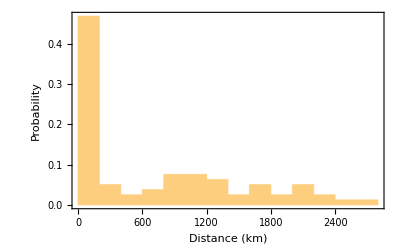

```mathematica
Histogram[Map[QuantityMagnitude[GeoDistance[#,UnitSystem->"km"]]&,corrStates],10,"Probability",Frame->True,FrameLabel->{"Distance (km)","Probability"}]
```

- Hypothesis: States that share the same electrical grid have correlated prices.

The United States electrical grid is divided in 8 separated regions by the North American Electric Reliability Corporation (NERC).

From this data alone a predictor may be constructed

The data of the coordinates of each grid was obtained from: https://www.google.com/maps/d/viewer?mid=16rZqG5BrdTh3Lpkhmjs6oafMPaM&hl=en&ll=62.92523564759902%2C-125.22216709375002&z=4

Although higher resolution data can be obtained from: https://public.opendatasoft.com/explore/dataset/nerc-regions/export/?flg=fr it proved to be impractical for the scope of this project because of the time needed to process it.

To see if states sharing the same grid have correlated prices we can plot the correlated states with the grid map as background

### Map of the grid: Parse the KML

The kernel has trouble parsing the KML file containing the grid coordinates. I will parse it manually. Also I will manually remove the grids from Alaska and Hawaii since I don’t have data relating to heating and cooling degree days in those areas.

```mathematica
data = Import[NotebookDirectory[]<>"nerc-regions.kml","XML"];
namesString = Drop[Flatten[Cases[data,XMLElement["name",{},n_]:>n,Infinity]],1];
coordinatesString = Cases[data,XMLElement["coordinates",{},c_]:> c,Infinity];

StringCoordToPolygon[s_String]:=Module[{flattenCoord,coord},
flattenCoord = ToExpression[StringSplit[s,Whitespace|","]];
coord = Partition[Drop[flattenCoord,{3,Length[flattenCoord],3}],2];
Polygon[coord]
];

nercAreas = Transpose[{namesString,Map[StringCoordToPolygon[First[#]]&,coordinatesString]}];
nercAreas = DeleteCases[nercAreas,{"ASCC",_}|{"HICC",_}];
```

Then I can plot them

```mathematica
names = nercAreas[[All,1]];
coordinates = nercAreas[[All,2]];
nercAreasForPlotting = Table[
{EdgeForm[Black],Tooltip[coordinates[[i]],names[[i]]]},{i,1Length[coordinates]}
];
GeoGraphics[nercAreasForPlotting]
```

-Graphics-

### A function to find the grid corresponding to a state

```mathematica
FindNercArea[state_]:=Module[{nercAreasNames,nercAreasCoord,testResults,pos},
nercAreasNames = nercAreas[[All,1]];
nercAreasCoord = nercAreas[[All,2]];
testResults = Map[GeoWithinQ[#,EntityValue[state,"Coordinates"]]&,nercAreasCoord];
If[Apply[Or,testResults]== True,
First[Extract[nercAreasNames,Position[testResults,True]]],
None
]
]
```

```mathematica
nercAreaOfState = Table[{s,FindNercArea[s]},{s,states}];
```

### High correlated states with the grid as background

```mathematica
Manipulate[
Show[
GeoGraphics[nercAreasForPlotting],
GeoListPlot[corrStates[[i]],PlotStyle->Directive[EdgeForm[Thick]]],
GeoRange->"Country"
],
{i,1,Length[corrStates],1},
SaveDefinitions->True
]
```

41% of the high correlated states share the same grid.

```mathematica
corrStatesAreas = Map[FindNercArea,corrStates,{2}];
N[Length[Select[corrStatesAreas,Apply[SameQ,#]&]]/Length[corrStatesAreas]]
```

0.417722

## Degree days

The degree days database is formatted as text separated with “|”.

```mathematica
shortStateRule = {"AL"->Entity["AdministrativeDivision",{"Alabama","UnitedStates"}],"AR"->Entity["AdministrativeDivision",{"Arkansas","UnitedStates"}],"AZ"->Entity["AdministrativeDivision",{"Arizona","UnitedStates"}],"CA"->Entity["AdministrativeDivision",{"California","UnitedStates"}],"CO"->Entity["AdministrativeDivision",{"Colorado","UnitedStates"}],"CT"->Entity["AdministrativeDivision",{"Connecticut","UnitedStates"}],"DE"->Entity["AdministrativeDivision",{"Delaware","UnitedStates"}],"FL"->Entity["AdministrativeDivision",{"Florida","UnitedStates"}],"GA"->Entity["AdministrativeDivision",{"Georgia","UnitedStates"}],"IA"->Entity["AdministrativeDivision",{"Iowa","UnitedStates"}],"ID"->Entity["AdministrativeDivision",{"Idaho","UnitedStates"}],"IL"->Entity["AdministrativeDivision",{"Illinois","UnitedStates"}],"IN"->Entity["AdministrativeDivision",{"Indiana","UnitedStates"}],"KS"->Entity["AdministrativeDivision",{"Kansas","UnitedStates"}],"KY"->Entity["AdministrativeDivision",{"Kentucky","UnitedStates"}],"LA"->Entity["AdministrativeDivision",{"Louisiana","UnitedStates"}],"MA"->Entity["AdministrativeDivision",{"Massachusetts","UnitedStates"}],"MD"->Entity["AdministrativeDivision",{"Maryland","UnitedStates"}],"ME"->Entity["AdministrativeDivision",{"Maine","UnitedStates"}],"MI"->Entity["AdministrativeDivision",{"Michigan","UnitedStates"}],"MN"->Entity["AdministrativeDivision",{"Minnesota","UnitedStates"}],"MO"->Entity["AdministrativeDivision",{"Missouri","UnitedStates"}],"MS"->Entity["AdministrativeDivision",{"Mississippi","UnitedStates"}],"MT"->Entity["AdministrativeDivision",{"Montana","UnitedStates"}],"NC"->Entity["AdministrativeDivision",{"NorthCarolina","UnitedStates"}],"ND"->Entity["AdministrativeDivision",{"NorthDakota","UnitedStates"}],"NE"->Entity["AdministrativeDivision",{"Nebraska","UnitedStates"}],"NH"->Entity["AdministrativeDivision",{"NewHampshire","UnitedStates"}],"NJ"->Entity["AdministrativeDivision",{"NewJersey","UnitedStates"}],"NM"->Entity["AdministrativeDivision",{"NewMexico","UnitedStates"}],"NV"->Entity["AdministrativeDivision",{"Nevada","UnitedStates"}],"NY"->Entity["AdministrativeDivision",{"NewYork","UnitedStates"}],"OH"->Entity["AdministrativeDivision",{"Ohio","UnitedStates"}],"OK"->Entity["AdministrativeDivision",{"Oklahoma","UnitedStates"}],"OR"->Entity["AdministrativeDivision",{"Oregon","UnitedStates"}],"PA"->Entity["AdministrativeDivision",{"Pennsylvania","UnitedStates"}],"RI"->Entity["AdministrativeDivision",{"RhodeIsland","UnitedStates"}],"SC"->Entity["AdministrativeDivision",{"SouthCarolina","UnitedStates"}],"SD"->Entity["AdministrativeDivision",{"SouthDakota","UnitedStates"}],"TN"->Entity["AdministrativeDivision",{"Tennessee","UnitedStates"}],"TX"->Entity["AdministrativeDivision",{"Texas","UnitedStates"}],"UT"->Entity["AdministrativeDivision",{"Utah","UnitedStates"}],"VA"->Entity["AdministrativeDivision",{"Virginia","UnitedStates"}],"VT"->Entity["AdministrativeDivision",{"Vermont","UnitedStates"}],"WA"->Entity["AdministrativeDivision",{"Washington","UnitedStates"}],"WI"->Entity["AdministrativeDivision",{"Wisconsin","UnitedStates"}],"WV"->Entity["AdministrativeDivision",{"WestVirginia","UnitedStates"}],"WY"->Entity["AdministrativeDivision",{"Wyoming","UnitedStates"}]};

FullDateToMonthly[date_]:=DateObject[Map[DateValue[date,#]&,{"Year","Month"}]];
ExtractDegreeDays[txt_]:=Module[{lines,dateStrings,dates,stateAndDDays,states,ddays,datesAndDDays,gatheredByMonth,datesAndDegreeDaysByMonth},
lines = StringSplit[txt,"\n"];
dateStrings = Drop[StringSplit[lines[[4]],"|"],1];
dates = Map[DateObject,dateStrings];
stateAndDDays = Map[StringSplit[#,"|"]&,Drop[lines,4]];
states =stateAndDDays[[All,1]] /. shortStateRule;
ddays = Map[Drop[#,1]&,stateAndDDays];
datesAndDDays = Map[Transpose[{dates,ToExpression[#]}]&,ddays];

datesAndDegreeDaysByMonth = Table[
gatheredByMonth = GatherBy[dh,DateValue[First[#],"Month"]&];
Map[{FullDateToMonthly[#[[1,1]]],Total[#[[All,2]]]}&,gatheredByMonth]
,{dh,datesAndDDays}
];

Transpose[{states,datesAndDegreeDaysByMonth}]
];

directories = Select[FileNames["*",NotebookDirectory[]<>"DegreeDays"],FileType[#]==Directory&];

heatingDegreesByStateYearly = Table[ExtractDegreeDays[Import[d<>"/StatesCONUS.Heating.txt"]],{d,directories}];
heatingDegreesByState= Table[{t[[1,1]],Flatten[t[[All,2]],1]},{t,Transpose[heatingDegreesByStateYearly]}];

coolingDegreesByStateYearly = Table[ExtractDegreeDays[Import[d<>"/StatesCONUS.Cooling.txt"]],{d,directories}];
coolingDegreesByState= Table[{t[[1,1]],Flatten[t[[All,2]],1]},{t,Transpose[coolingDegreesByStateYearly]}];
```

In order to find correlations between electricity prices it is necessary to match the data by date.

```mathematica
dates = Sort[electricityPricesByDate[[All,1]]];
SelectInDateRange[data_]:= Select[data,First[dates]≤First[#]≤ Last[dates]&];
heatingDegreesByState = MapAt[SelectInDateRange,heatingDegreesByState,{All,2}];
coolingDegreesByState = MapAt[SelectInDateRange,coolingDegreesByState,{All,2}];
heatingDegreesByState = SortBy[heatingDegreesByState,First];
coolingDegreesByState = SortBy[coolingDegreesByState,First];
```

Plots

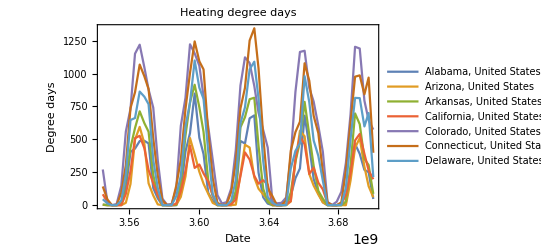

```mathematica
pltData = Take[heatingDegreesByState,7];
DateListPlot[pltData[[All,2]],FrameLabel->{"Date", "Degree days"},PlotLegends->pltData[[All,1]],PlotLabel->"Heating degree days"]
```

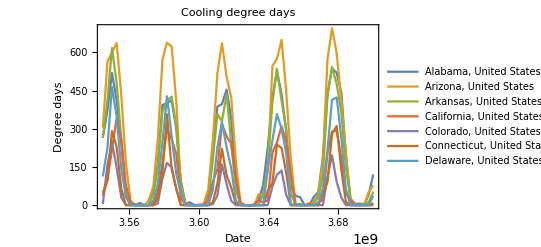

```mathematica
pltData = Take[coolingDegreesByState,7];
DateListPlot[pltData[[All,2]],FrameLabel->{"Date", "Degree days"},PlotLegends->pltData[[All,1]],PlotLabel->"Cooling degree days"]
```

## Correlation between degree days and electricity prices

One might expect that both heating degree days and cooling degree days would increase electricity consumption, also increasing the price by the effect of increased demand. This is however not accurate, as the following plots show, heating and cooling degree days not always increase the price, and surprisingly in some cases actually reduce the price. This might be explained by differences in infrastructure, economy or electricity generation of each state. For example, anti correlations in heating degree days could be because in cold days there is less need to maintain the ventilation needed for industrial processes. In cooling degree days might be because renewable electric sources produce more electricity in hot days.

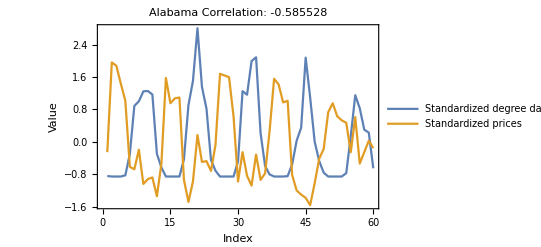
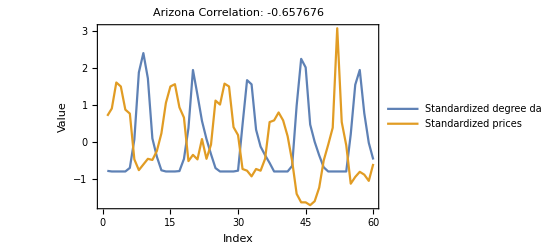
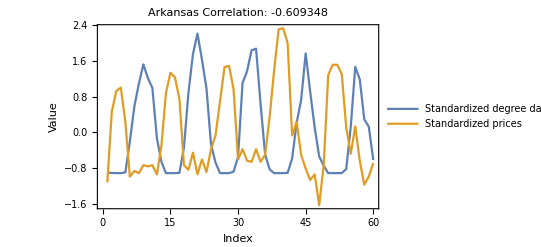
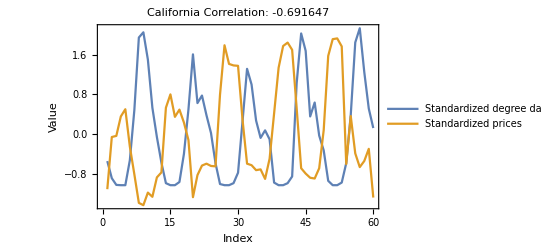
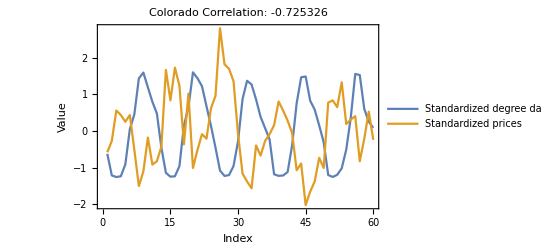
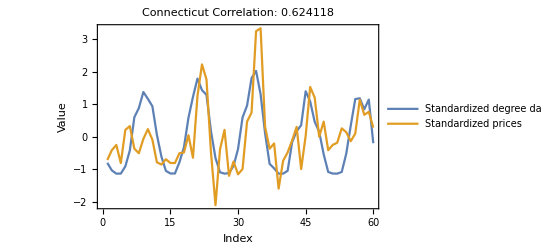
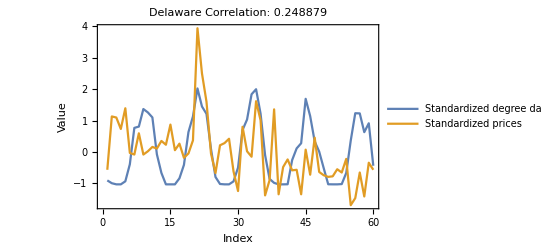
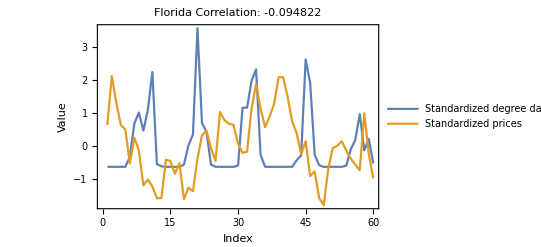
Heating degree days |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

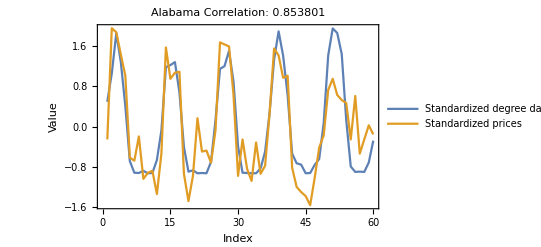
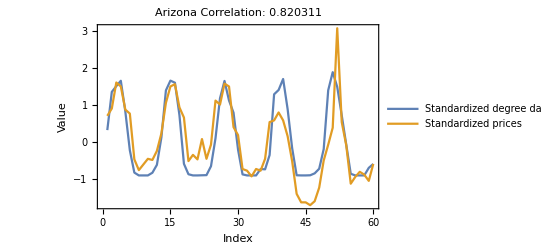
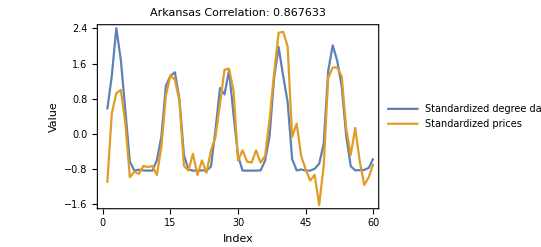
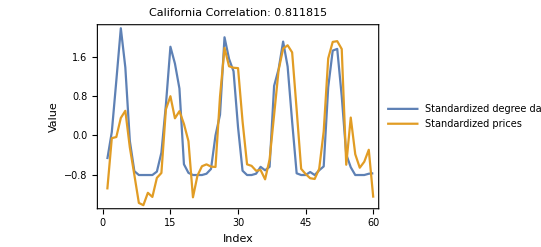
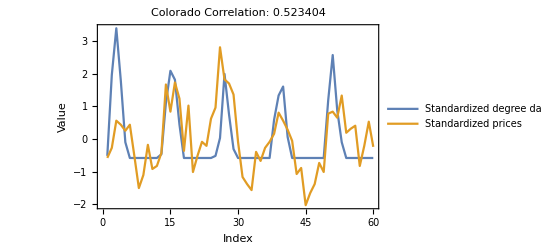
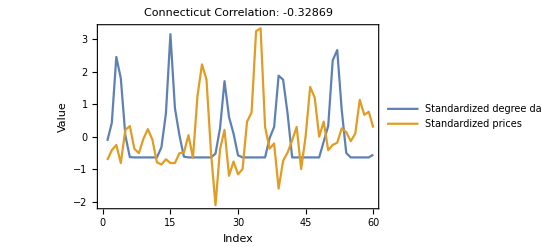
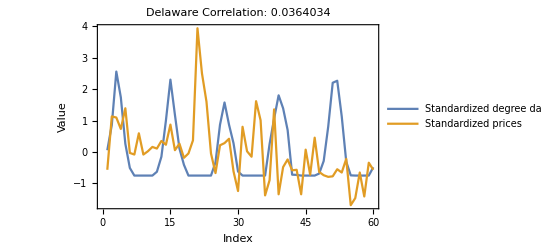
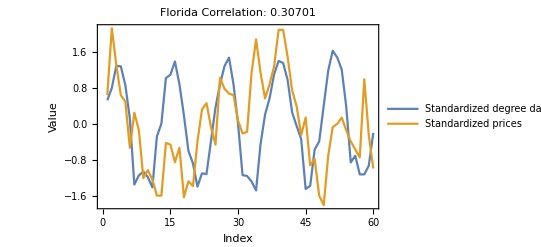
Cooling degree days |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
DegreeDaysCorrPlots[data_]:=Module[{states, degreeDays, prices, stateName, corrString},
states = electricityPricesByState[[All,1]];
Table[
degreeDays = data[[s,2,All,2]];
prices = electricityPricesByState[[s,2,All,2]];
stateName = StringDelete[states[[s]]["Name"], ", United States"];
corrString = "Correlation: "<>ToString[Correlation[degreeDays,prices]];

ListLinePlot[{Standardize[degreeDays],Standardize[prices]},Frame->True,FrameLabel->{"Index","Value"},PlotLegends->{"Standardized degree days","Standardized prices"},
PlotLabel->stateName<>"\n"<>corrString
]
,{s,1,Length[states]}
]
];

heatingDegreeDaysCorrPlots = DegreeDaysCorrPlots[heatingDegreesByState];
coolingDegreeDaysCorrPlots = DegreeDaysCorrPlots[coolingDegreesByState];
heatingGridElements = Join[{{Style["Heating degree days",20,Red],SpanFromLeft}},Partition[heatingDegreeDaysCorrPlots,UpTo[4]]];
coolingGridElements = Join[{{Style["Cooling degree days",20,Blue],SpanFromLeft}},Partition[coolingDegreeDaysCorrPlots,UpTo[4]]];

Grid[heatingGridElements,Frame->All]
Grid[coolingGridElements,Frame->All]
```

Since the correlation between heating degree and cooling degree days are different for each state and depends on it’s properties one could assume that they are fixed, or at least that they change very slowly in time. Let’s suppose two values α and β of the “strength” of heating degree days and cooling degree days respect to price changes. I can find the optimum values of α and β to maximize correlation between degree days and electricity prices. Assuming that the properties of the states don’t change in a short timespan these α and β will be fixed in time.

```mathematica
stateαβparamsWCorr = Table[
prices = electricityPricesByState[[s,2,All,2]];
hd = heatingDegreesByState[[s,2,All,2]];
cd = coolingDegreesByState[[s,2,All,2]];
αβtbl =Flatten[Table[{α,β,Correlation[{α ,β }.{hd,cd},prices]},{α,-1,1,0.03},{β,-1,1,0.03}],1];
{states[[s]],First[MaximalBy[αβtbl,Last]]}
,{s,1,Length[states]}
];

stateαβparams= MapAt[Drop[#,-1]&,stateαβparamsWCorr,{All,2}];
GeoRegionValuePlot[Transpose[{stateαβparams[[All,1]],stateαβparams[[All,2]][[All,1]]}],ColorFunction->"TemperatureMap",PlotLabel->"Heating degree days"]
GeoRegionValuePlot[Transpose[{stateαβparams[[All,1]],stateαβparams[[All,2]][[All,2]]}],ColorFunction->"TemperatureMap",PlotLabel->"Cooling degree days"]
```

-Graphics-

-Graphics-

## GDP of states

One factor that might be related to prices is the GDP of the state. I chose to use this because is a measure of how well the economy is doing, and this affect wages and investment in infrastructure.

```mathematica
DateToYearly[date_]:=DateObject[{DateValue[date,"Year"]}];

dates = Sort[electricityPricesByDate[[All,1]]];
FindStateGDPByMonth[state_,datefrom_,dateto_]:=Module[{gdpTS,gdpValues,datesMissing,fillArr},
gdpTS = EntityValue[state,EntityProperty["AdministrativeDivision","GrossDomesticProduct",{"Date"->Interval[{DateToYearly[datefrom],DateToYearly[dateto]}]}]];
gdpValues = MapAt[DateToYearly,Normal[QuantityMagnitude[gdpTS]],{All,1}];(* Somehow when the TimeSeries is created, it returns full dates (that include the day). I map it again to yearly dates. *)

(* Adjust the magnitude so I don't get a big number that crashes the predictor *)
gdpValues = MapAt[#/10^10&,gdpValues,{All,2}];
gdpValues = Flatten[Table[Map[If[DateWithinQ[g[[1]],#],{#,g[[2]]},Nothing]& ,dates],{g,gdpValues}],1];

(* Since GDP of current year can't be obtained I will use the last known value *)
datesMissing = Complement[dates,gdpValues[[All,1]]];
fillArr = ConstantArray[Last[gdpValues][[2]],Length[datesMissing]];
gdpValues = Join[gdpValues,Transpose[{datesMissing,fillArr}]];

Return[gdpValues];
];
gdps = Table[{s,FindStateGDPByMonth[s,First[dates],Last[dates]]},{s,states}];
```

```mathematica
Manipulate[GeoRegionValuePlot[Transpose[{gdps[[All,1]],gdps[[All,2,t]][[All,2]]}],PlotLabel->DateString[dates[[t]]],ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Log[#/100+1]]&)],{t,1,Length[dates],1}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Symbol[],Symbol[]} cannot be transposed.

Part::partd: Part specification dates⟦1⟧ is longer than depth of object.

DateString::arg: Argument dates⟦1⟧ cannot be interpreted as a date or time input or as a date string format.

Part::partd: Part specification dates⟦1⟧ is longer than depth of object.

DateString::arg: Argument dates⟦1⟧ cannot be interpreted as a date or time input or as a date string format.

GeoRegionValuePlot::noents: no valid location -> value pairs found

Infinity::indet: Indeterminate expression -∞+∞ encountered.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Symbol[],Symbol[]} cannot be transposed.

Part::partd: Part specification dates⟦1⟧ is longer than depth of object.

DateString::arg: Argument dates⟦1⟧ cannot be interpreted as a date or time input or as a date string format.

GeoRegionValuePlot::noents: no valid location -> value pairs found

Infinity::indet: Indeterminate expression -∞+∞ encountered.

## Commodities price

Since electric plants rely on commodities like natural gas or coal, their prices affect directly the electricity. The prices of commodities can be found on public databases like FRED II or the EIA

Source: https://www.eia.gov/dnav/ng/hist/n3035us3m.htm

```mathematica
naturalGasIndustrialPriceAll = Import[NotebookDirectory[]<>"CommodityPrices/United_States_Natural_Gas_Industrial_Price.csv"];
naturalGasIndustrialPriceAll = SortBy[MapAt[DateObject,naturalGasIndustrialPriceAll,{All,1}],First];
dates = Sort[electricityPricesByDate[[All,1]]];
naturalGasIndustrialPrice = Select[naturalGasIndustrialPriceAll,First[dates]≤ #[[1]]≤ Last[dates]&];
```

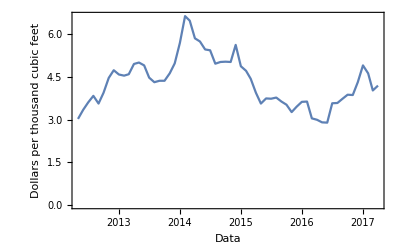

```mathematica
DateListPlot[naturalGasIndustrialPrice,FrameLabel->{"Data","Dollars per thousand cubic feet"}]
```

Natural gas price in the US (averaged). Source: https://www.quandl.com/collections/markets/coal

```mathematica
FullDateToMonthly[date_]:=DateObject[Map[DateValue[date,#]&,{"Year","Month"}]];
coalPrice = Import[NotebookDirectory[]<>"CommodityPrices/EIA-COAL.csv"];
coalPrice = Map[{FullDateToMonthly[First[#]],Mean[Drop[#,1]]}&,Drop[coalPrice,1]];
coalPrice = SortBy[coalPrice,First];
coalPrice = Select[coalPrice,First[dates]≤ First[#]≤ Last[dates]&];
```

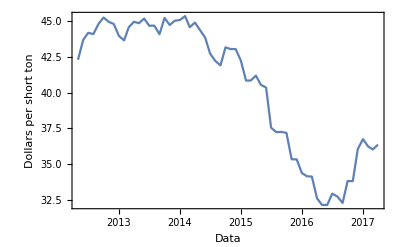

```mathematica
DateListPlot[coalPrice,FrameLabel->{"Data","Dollars per short ton"}]
```

## Dataset for training

With all the collected data I can construct my database for training. If the data is useful and related to the actual factors involved in determining the price of electricity the predictor will be able to return reasonable results.

```mathematica
examples = 
Table[
gas = naturalGasIndustrialPrice[[All,2]];
gdp = gdps[[s,2,All,2]];
prices =electricityPricesByState[[s,2,All,2]];
hdDays = N@heatingDegreesByState[[s,2,All,2]];
cdDays = N@coolingDegreesByState[[s,2,All,2]];
dDays = N@stateαβparams[[s,2]].{hdDays,cdDays};
gridArr = ConstantArray[nercAreaOfState[[s,2]],{Length[prices]}];
features = Transpose[{gridArr,dDays,gas,gdp}];
stateTraininSet = MapThread[#1->#2&,{features,prices}],
{s,1,Length[states]}
];
examples = Flatten[examples,1];

(* To fix the bug in randomforest *)
examples=MapAt[#+RandomReal[0.0001]&,examples,{All,2}];
examples=MapAt[#+RandomReal[0.0001]&,examples,{All,1,2;;3}];
```

```mathematica
examples=RandomSample[examples];
trainingSet = Take[examples,Floor[0.8*Length[examples]]];
validationSet = Drop[examples,Floor[0.8*Length[examples]]];
```

Search for the best predictor

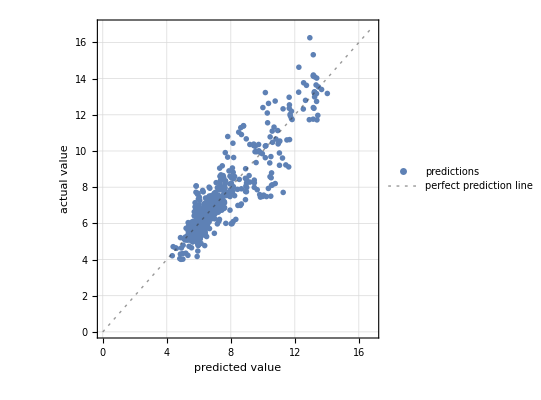
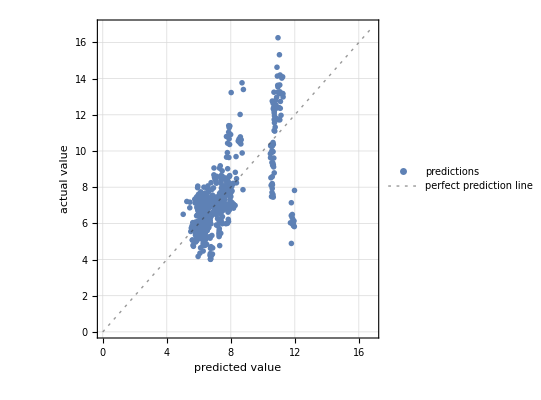
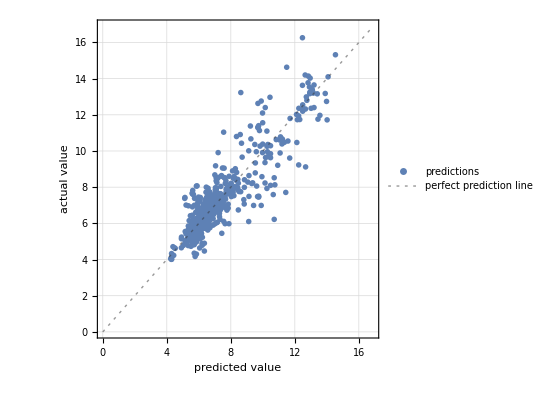
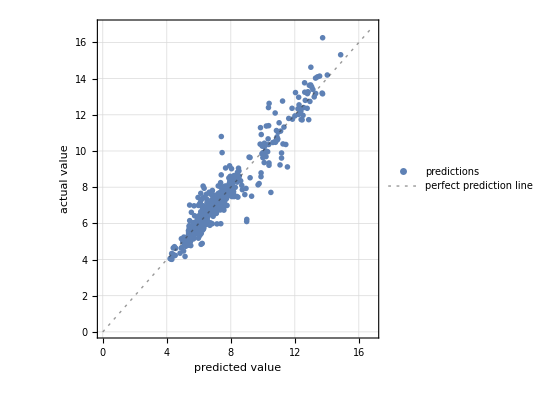

{0.896166,1.53107,0.96011,0.593298}

```mathematica
predictors=Map[Predict[trainingSet,Method-> #,PerformanceGoal->"Quality"]&,{"GaussianProcess", "LinearRegression", "NearestNeighbors", "RandomForest"}];
Map[PredictorMeasurements[#,validationSet]["ComparisonPlot"]&,predictors]
Map[PredictorMeasurements[#,validationSet]["StandardDeviation"]&,predictors]
```

Seems that the random forest is the most accurate. I can repeat the training many times in order to obtain a distribution of the standard deviations.

0.58995

0.0416732

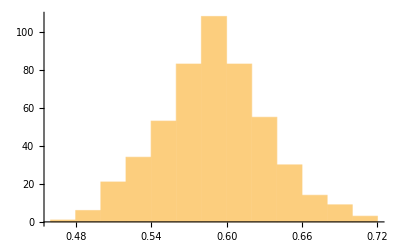

```mathematica
σs = Table[
examples=RandomSample[examples];
trainingSet = Take[examples,Floor[0.8*Length[examples]]];
validationSet = Drop[examples,Floor[0.8*Length[examples]]];
p = Predict[trainingSet,Method->"RandomForest"];
pm = PredictorMeasurements[p,validationSet];
pm["StandardDeviation"]
,{500}
];
Mean[σs]
StandardDeviation[σs]
Histogram[σs]
```

This training set produces better results

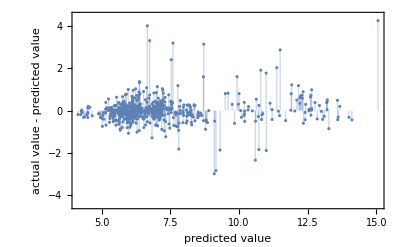

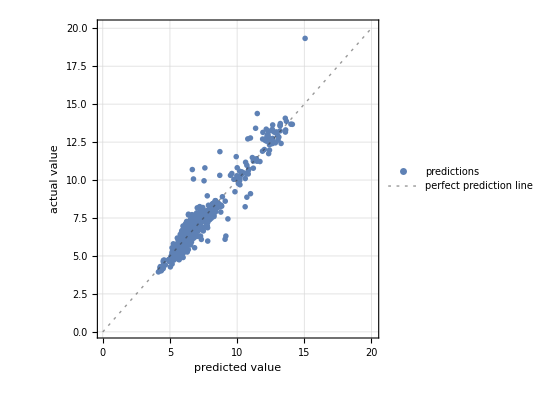

0.621648

```mathematica
examples = 
Table[
coal = coalPrice[[All,2]];
gas = naturalGasIndustrialPrice[[All,2]];
gdp = gdps[[s,2,All,2]];
prices =electricityPricesByState[[s,2,All,2]];
hdDays = N@heatingDegreesByState[[s,2,All,2]];
cdDays = N@coolingDegreesByState[[s,2,All,2]];
dDays = N@stateαβparams[[s,2]].{hdDays,cdDays};
gridArr = ConstantArray[nercAreaOfState[[s,2]],{Length[prices]}];
features = Transpose[{gridArr,dDays,coal,gdp}];
stateTraininSet = MapThread[#1->#2&,{features,prices}],
{s,1,Length[states]}
];
examples = Flatten[examples,1];

(* To fix the bug in randomforest *)
examples=MapAt[#+RandomReal[0.0001]&,examples,{All,2}];
examples=MapAt[#+RandomReal[0.0001]&,examples,{All,1,2;;3}];

examples=RandomSample[examples];
trainingSet = Take[examples,Floor[0.8*Length[examples]]];
validationSet = Drop[examples,Floor[0.8*Length[examples]]];

p = Predict[trainingSet,PerformanceGoal->"Quality",Method->"RandomForest"];
pm = PredictorMeasurements[p,validationSet];
pm["ResidualPlot"]
pm["ComparisonPlot"]
pm["StandardDeviation"]
```

## Safeguard for kernel crashing

```mathematica
DumpSave[NotebookDirectory[]<>"state.mx","Global`"]
```

{Global`}

```mathematica
Get[NotebookDirectory[]<>"state.mx"]
```